```mathematica
NumberOfAtoms=2;
NumberOfSubspaces = 2; 
NumberOfModes = 1;
ExcitedLevel[Subspace_]=NumberOfSubspaces+Subspace;
```

#### The initial state

```mathematica
cons[Atom_,Subspace_,Type_]:=
Module[{a},
a=ConstantArray[KroneckerDelta[Subspace,1](1+Type,2)+KroneckerDelta[Subspace,2](1+Type,1),NumberOfAtoms+NumberOfModes];
a[[Atom]]=ExcitedLevel[Subspace];
a[[NumberOfAtoms+1;;]]=0;
a ];
```

```mathematica
For[m=1,m<=NumberOfAtoms,m++,

(* Subspace I *)
ψI[m]= cons[m,1,1];

(* Subspace II *)
ψII[m]= cons[m,1,2];

(* Subspace III *)
ψIII[m]= cons[m,2,1];

(* Subspace IV *)
ψIV[m]= cons[m,2,2];
];

ClearAll[m];

InitialStates=(ψI[#]&/@Range[NumberOfAtoms])~Join~(ψII[#]&/@Range[NumberOfAtoms])~Join~(ψIII[#]&/@Range[NumberOfAtoms])~Join~(ψIV[#]&/@Range[NumberOfAtoms]);
dimZO=Dimensions[InitialStates][[1]];
```

#### Transitions

```mathematica
NextStates[KnownStates_,BoundaryStates_]:=
Module[
{a,b,NextKnown,NextBoundary},
b={};
Do[(* Go through all the boundary states *)

Do[(* Check the states of all the atoms one by one *)

(* Subscript[E, 1] can change to Subscript[G, 1] -- emitting a photon *)
a =BoundaryStates[[m]];
If[
a[[k]]==ExcitedLevel[1],
a[[k]]=1;  
a[[NumberOfAtoms+1]]= a[[NumberOfAtoms+1]]+1;
b=Append[b,a];
];

(* Subscript[E, 2] can change to Subscript[G, 1]  -- no photons emitted yet *)
a =BoundaryStates[[m]];
If[
a[[k]]==ExcitedLevel[2],
a[[k]]=1;  ;
b=Append[b,a];
];

(* Subscript[G, 1] can change to Subscript[E, 2] -- classical light absorbed *)
a =BoundaryStates[[m]];
If[a[[k]]==1,
a[[k]]=ExcitedLevel[2];
b=Append[b,a]];

(* Subscript[G, 1] can change to Subscript[E, 1]-- absorbing a *)
If[a[[k]] =1&&a[[NumberOfAtoms+1]]>0,
a[[k]]=ExcitedLevel[1];  
a[[NumberOfAtoms+1]]= a[[NumberOfAtoms+1]]-1;
b=Append[b,a];
]

,{k,1,NumberOfAtoms}];

,{m,1,Dimensions[BoundaryStates][[1]]}];

b= DeleteDuplicates[b]; (* These are the all the possible next boundary states if they are not already known *)

NextKnown =KnownStates~Join~b;
NextKnown = DeleteDuplicates[NextKnown];

If[Dimensions[NextKnown][[1]]>Dimensions[KnownStates][[1]],
NextBoundary = NextKnown[[Dimensions[KnownStates][[1]]+1;;]]
,NextBoundary={}
];
{NextKnown,NextBoundary}

];
```

#### States first-order transition away from the initial state

```mathematica
{Known, FirstOrderStates}= NextStates[InitialStates,InitialStates];
dimFO=Dimensions[FirstOrderStates][[1]];
```

#### States second-order transition away from the initial state

```mathematica
{Known, SecondOrderStates}= NextStates[Known,FirstOrderStates];
dimSO=Dimensions[SecondOrderStates][[1]];
```

```mathematica
dimK = Dimensions[Known][[1]];
```

#### Graph Plot of the Hilbert space

```mathematica
IsEdge[ψ1_,ψ2_]:=Module[{photonEmAbs,diffNum,a},

diffNum=0;
photonEmAbs=0;
a=True;

For[k=1,k<=NumberOfAtoms,k++,

If[ψ1[[k]]!=ψ2[[k]],
diffNum = diffNum +1
];

If[(ψ1[[k]]==3&&ψ2[[k]]==4)∨(ψ1[[k]]==4&&ψ2[[k]]==3),
a=False;
];

If[(ψ1[[k]]==1&&ψ2[[k]]==2)∨(ψ1[[k]]==2&&ψ2[[k]]==1),
a=False;
];

If[(ψ1[[k]]==1&&ψ2[[k]]==3)∨(ψ1[[k]]==3&&ψ2[[k]]==1),
photonEmAbs= photonEmAbs+Sign[ψ1[[k]]-ψ2[[k]]] +ψ1[[NumberOfAtoms+1]]-ψ2[[NumberOfAtoms+1]];
];

If[ψ1[[k]]==3&&ψ2[[k]]==1,
photonEmAbs= photonEmAbs+1 +ψ1[[NumberOfAtoms+1]]-ψ2[[NumberOfAtoms+1]];
];

If[(ψ1[[k]]==1&&ψ2[[k]]==4)∨(ψ1[[k]]==4&&ψ2[[k]]==1),
photonEmAbs= photonEmAbs+0 +ψ1[[NumberOfAtoms+1]]-ψ2[[NumberOfAtoms+1]];
];

If[(ψ1[[k]]==2&&ψ2[[k]]!=2)∨(ψ2[[k]]==2&&ψ1[[k]]!=2),
a=False
];


];
 
a&&(diffNum==1)&&(photonEmAbs==0)

];

StateLabel[ψ_]:=Module[{a},
a={};
For [k=1,k<=NumberOfAtoms,k++,
a=Append[a,Piecewise[{{"G_1 ", ψ[[k]]==1}, {"G_2 ", ψ[[k]]==2}, {"E_1 ", ψ[[k]]==3}, {"E_2 ", ψ[[k]]==4}}]]
];
a=Append[a,ψ[[NumberOfAtoms+1]]];
Row@a
];
```

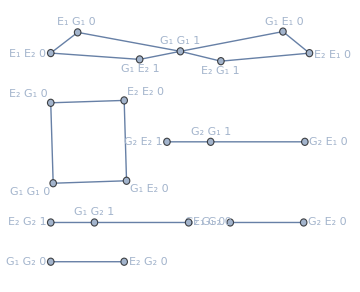

```mathematica
elength={};
FormGraph=Module[{graph},
graph={};
Do[
Do[
If[IsEdge[Known[[i]],Known[[f]]],
AppendTo[graph,i<->f];
AppendTo[elength,If[Known[[i,NumberOfAtoms+1]]==Known[[f,NumberOfAtoms+1]],1,2]
]
]
,{f,i+1,dimK}];
,{i,1,dimK}];
graph
];

graph=Graph[FormGraph,VertexLabels->Table[i->StateLabel[Known[[i]]],{i,1,dimK}],(*GraphLayout->"SpringEmbedding",*)VertexLabelStyle->Medium,VertexSize->Medium,ImageSize->Medium,EdgeWeight->elength,GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}]
```

(1<->9
1<->10
2<->9
2<->11
3<->12
4<->13
5<->14
6<->15
7<->16
7<->17
8<->16
8<->17
9<->18
9<->19
10<->19
11<->18
12<->20
13<->21)

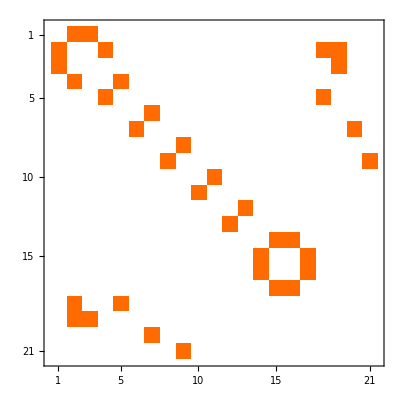

```mathematica
MatrixForm[FormGraph]
MatrixPlot[AdjacencyMatrix[FormGraph]]
```

#### Energies

```mathematica
g1[1]=g1[2]=ωg1;
g2[1]=g2[2]=ωg2;
e1[1]=e1[2]=ωe1;
e2[1]=e2[2]=ωe2;
ℏ=1;
Ωal[1]=Ωal[2]=Ω;

ωk[ψ_]:=Module[{a},
a=0;
Do[
a=a+Piecewise[{{g1[m], ψ[[m]]==1}, {g2[m], ψ[[m]]==2}, {e1[m], ψ[[m]]==3}, {e2[m], ψ[[m]]==4}}]

,{m,1,NumberOfAtoms}];

ωph ψ[[NumberOfAtoms+1]]+a
];

ωfi[ψf_,ψi_]:=ωk[ψf]-ωk[ψi];
```

#### Perturbed Hamiltonian

```mathematica
ClearAll[ωg1,ωph,Δ,ωe1,υ,ωe2,ωg2,Ω,A];
ωe1=ωg1+ωph+Δ;
ωe2=ωg1+Δ+υ;

Vfi[f_,i_,t_]:=Module[{ψf,ψi,a},
a=0;
If[IsEdge[Known[[i]],Known[[f]]],
ψi=Known[[i]];
ψf=Known[[f]];

Do[
a= a
+Abs[Known[[f,m]]  -Known[[i,m]]],NumberOfSubspaces ℏ Ωal[m]/2 ⅇ^(ⅈ t ωfi[ψf,ψi])
+Abs[Known[[f,m]]  -Known[[i,m]]],NumberOfSubspaces+1 ℏ  A  ⅇ^(-ⅈ Sign[ωfi[ψf,ψi]] t υ)(*2 Cos[υ t]*) ⅇ^(ⅈ t ωfi[ψf,ψi])

,{m,1,NumberOfAtoms}];
];
a
];
Vmatrix[t_] = Simplify[Table[Vfi[f,i,t],{f,1,dimK},{i,1,dimK}],ϕ∈Reals&&Δ>0&&υ>0&&υ>Δ];
```

#### Initial coefficients

```mathematica
X0=ConstantArray[0,dimK];
choice =1;
list=Piecewise[{{{1,1,0,0,0,0,-ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ)}, choice==1(* Heralding on Not Subscript[G, 2] *)}, {{0,0,1,1,ⅇ^(ⅈ ϕ),ⅇ^(ⅈ ϕ),0,0}, choice==2 (* Heralding on Not Subscript[G, 1] *)}, {{1,1,1,1,ⅇ^(ⅈ ϕ),ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ)}, choice==3 (* Without heralding *)}}]
X0[[1;;8]]=list;
X0=X0/Norm[X0];
```

{1,1,0,0,0,0,-ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ)}

#### Computing Perturbed coefficients

```mathematica
Ci[k_,t_]:=Simplify[Piecewise[{{X0, k<=0}, {(-ⅈ/ℏ) ∫_0^t (Vmatrix[τ].Ci[k-1,τ])ⅆτ, k>=0}}],ϕ∈Reals&&Δ>0&&υ>0&&υ>Δ];
(*Ci[0,t]//MatrixForm
Ci[1,t]//MatrixForm
Ci[2,t]//MatrixForm*)
norm = Norm[Ci[0,t]+Ci[1,t]+Ci[2,t]];
```

#### C^(k) for heralding on Not G_2

(1/2
1/2
0
0
0
0
-ⅇ^(ⅈ ϕ)/2
-ⅇ^(ⅈ ϕ)/2
0
0
0
0
0
0
0
0
0
0
0
0
0)

(0
0
0
0
0
0
0
0
-(Ω-ⅇ^(-ⅈ t Δ) Ω)/(2 Δ)
-(A (-1+ⅇ^(ⅈ t Δ)))/(2 Δ)
-(A (-1+ⅇ^(ⅈ t Δ)))/(2 Δ)
0
0
0
0
(A ⅇ^(-ⅈ t Δ+ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)))/Δ
(A ⅇ^(ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)))/Δ
0
0
0
0)

(-(ⅈ (A^2 (-2 ⅈ+2 ⅈ ⅇ^(-ⅈ t Δ)-2 t Δ)+(-ⅈ+ⅈ ⅇ^(ⅈ t Δ)+t Δ) Ω^2))/(4 Δ^2)
-(ⅈ (A^2 (-2 ⅈ+2 ⅈ ⅇ^(-ⅈ t Δ)-2 t Δ)+(-ⅈ+ⅈ ⅇ^(ⅈ t Δ)+t Δ) Ω^2))/(4 Δ^2)
0
0
0
0
-(2 A^2 ⅇ^(ⅈ ϕ) (-1+Cos[t Δ]))/Δ^2
-(2 A^2 ⅇ^(ⅈ ϕ) (-1+Cos[t Δ]))/Δ^2
0
0
0
0
0
0
0
0
0
(A Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/(4 Δ^2)
(A Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/(4 Δ^2)
0
0)

#### C^(k) for heralding on Not G_1

(0
0
1/2
1/2
ⅇ^(ⅈ ϕ)/2
ⅇ^(ⅈ ϕ)/2
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

(0
0
0
0
0
0
0
0
0
0
0
-(Ω-ⅇ^(-ⅈ t Δ) Ω)/(4 Δ)
-(Ω-ⅇ^(-ⅈ t Δ) Ω)/(4 Δ)
-(A ⅇ^(-ⅈ t Δ+ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)))/(2 Δ)
-(A ⅇ^(-ⅈ t Δ+ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)))/(2 Δ)
0
0
0
0
0
0)

(0
0
((-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω^2)/(8 Δ^2)
((-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω^2)/(8 Δ^2)
(A^2 ⅇ^(ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ))/(2 Δ^2)
(A^2 ⅇ^(ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ))/(2 Δ^2)
0
0
0
0
0
0
0
0
0
0
0
0
0
(A (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/(4 Δ^2)
(A (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/(4 Δ^2))

#### State Solution and Electric Field Matrix

```mathematica
Xsol[t_]=(Ci[0,t]+Ci[1,t]+Ci[2,t])/norm(ⅇ^(-ⅈ t/ℏ ωk[Known[[#]]])&/@Range[dimK]);
ClearAll[ϕ];
Φ[k_] :=Known[[k]];

Ψ[ϕ_,t_]=Xsol[t]  ;

ElectricFieldMatrixElements[p_,q_]:=Module[{ϕ1,ϕ2,a},
ϕ1=Φ[p];
ϕ2=Φ[q];
a=0;
If[ϕ1[[1;;NumberOfAtoms]]==ϕ2[[1;;NumberOfAtoms]],
a=Abs[ϕ1[[NumberOfAtoms+1]]-ϕ2[[NumberOfAtoms+1]]] 
];
a];

ElectricFieldMatrix = Table[ElectricFieldMatrixElements[p,q],{p,1,dimK},{q,1,dimK}];
```

Xunnormed=FullSimplify[(Ci[0,t]+Ci[1,t]+Ci[2,t])/1(ⅇ^(-ⅈ t/ℏ ωk[Known[[#]]])&/@Range[dimK]),ϕ∈Reals&&Δ>0&&t>0&&Ω>0&&A>0&&υ>Δ&&ωph>Δ]

{(ⅇ^(-ⅈ t (Δ+2 ωg1+ωph)) (2+(2 A^2 (-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ)+(-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω^2)/Δ^2))/(4 √2),(ⅇ^(-ⅈ t (Δ+2 ωg1+ωph)) (2+(2 A^2 (-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ)+(-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω^2)/Δ^2))/(4 √2),(ⅇ^(-ⅈ t (Δ+ωg1+ωg2+ωph)) (4 Δ^2+(-1+ⅇ^(ⅈ t Δ)) Ω^2-ⅈ t Δ Ω^2))/(8 √2 Δ^2),(ⅇ^(-ⅈ t (Δ+ωg1+ωg2+ωph)) (4 Δ^2+(-1+ⅇ^(ⅈ t Δ)) Ω^2-ⅈ t Δ Ω^2))/(8 √2 Δ^2),(ⅇ^(ⅈ (ϕ-t (Δ+υ+ωg1+ωg2))) (Δ^2+A^2 (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ)))/(2 √2 Δ^2),(ⅇ^(ⅈ (ϕ-t (Δ+υ+ωg1+ωg2))) (Δ^2+A^2 (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ)))/(2 √2 Δ^2),-(ⅇ^(ⅈ (ϕ-t (Δ+υ+2 ωg1))) (-4 A^2+Δ^2+4 A^2 Cos[t Δ]))/(2 √2 Δ^2),-(ⅇ^(ⅈ (ϕ-t (Δ+υ+2 ωg1))) (-4 A^2+Δ^2+4 A^2 Cos[t Δ]))/(2 √2 Δ^2),-(ⅇ^(-ⅈ t (Δ+2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(2 √2 Δ),-(A ⅇ^(-ⅈ t (2 Δ+υ+2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),-(A ⅇ^(-ⅈ t (2 Δ+υ+2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),-(ⅇ^(-ⅈ t (Δ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(4 √2 Δ),-(ⅇ^(-ⅈ t (Δ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(4 √2 Δ),-(A ⅇ^(ⅈ (ϕ-t (Δ+ωg1+ωg2))) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),-(A ⅇ^(ⅈ (ϕ-t (Δ+ωg1+ωg2))) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),(A ⅇ^(ⅈ (ϕ-t (Δ+2 ωg1))) (-1+ⅇ^(ⅈ t Δ)))/(√2 Δ),(A ⅇ^(ⅈ (ϕ-2 t (Δ+υ+ωg1))) (-1+ⅇ^(ⅈ t Δ)))/(√2 Δ),(A ⅇ^(-ⅈ t (Δ+υ+2 ωg1+ωph)) Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/(4 √2 Δ^2),(A ⅇ^(-ⅈ t (Δ+υ+2 ωg1+ωph)) Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/(4 √2 Δ^2),(A ⅇ^(-ⅈ t (Δ+υ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/(4 √2 Δ^2),(A ⅇ^(-ⅈ t (Δ+υ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/(4 √2 Δ^2)}

norm^2

1/4 Abs[(A (-1+ⅇ^(ⅈ t Δ)))/Δ]^2+3/4 ⅇ^(2 Im[t Δ]-2 Im[ϕ]) Abs[(A (-1+ⅇ^(ⅈ t Δ)))/Δ]^2+1/2 ⅇ^(-2 Im[ϕ]) Abs[(A (-1+ⅇ^(ⅈ t Δ)))/Δ]^2+2 Abs[ⅇ^(ⅈ ϕ)/(2 √2)+(A^2 ⅇ^(ⅈ ϕ) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ))/(2 √2 Δ^2)]^2+3/16 Abs[((1-ⅇ^(-ⅈ t Δ)) Ω)/Δ]^2+1/16 Abs[(A (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/Δ^2]^2+2 Abs[1/(2 √2)+((-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω^2)/(8 √2 Δ^2)]^2+2 Abs[1/(2 √2)+(ⅈ (A^2 (2 ⅈ-2 ⅈ ⅇ^(-ⅈ t Δ)+2 t Δ)-ⅈ (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω^2))/(4 √2 Δ^2)]^2+1/16 Abs[(A Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/Δ^2]^2+2 Abs[-ⅇ^(ⅈ ϕ)/(2 √2)-(√2 A^2 (-1+Cos[t Δ]) (Cos[ϕ]+ⅈ Sin[ϕ]))/Δ^2]^2

RHvec = FullSimplify[ElectricFieldMatrix . Xunnormed, ϕ ∈ Reals && Δ > 0 && t > 0 && Ω > 0 && A > 0 && υ > Δ && ωph > Δ]

{0,0,0,0,(A ⅇ^(-ⅈ t (Δ+υ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/(4 √2 Δ^2),(A ⅇ^(-ⅈ t (Δ+υ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ) Ω)/(4 √2 Δ^2),(A ⅇ^(-ⅈ t (Δ+υ+2 ωg1+ωph)) Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/(4 √2 Δ^2),(A ⅇ^(-ⅈ t (Δ+υ+2 ωg1+ωph)) Ω (-3-ⅈ t Δ+3 Cos[t Δ]+ⅈ Sin[t Δ]))/(4 √2 Δ^2),(A ⅇ^(ⅈ (ϕ-t (Δ+2 ωg1))) (-1+ⅇ^(ⅈ t Δ)))/(√2 Δ),0,0,-(A ⅇ^(ⅈ (ϕ-t (Δ+ωg1+ωg2))) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),-(A ⅇ^(ⅈ (ϕ-t (Δ+ωg1+ωg2))) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),-(ⅇ^(-ⅈ t (Δ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(4 √2 Δ),-(ⅇ^(-ⅈ t (Δ+ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(4 √2 Δ),-(ⅇ^(-ⅈ t (Δ+2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(2 √2 Δ),0,-(ⅇ^(ⅈ (ϕ-t (Δ+υ+2 ωg1))) (-4 A^2+Δ^2+4 A^2 Cos[t Δ]))/(2 √2 Δ^2),-(ⅇ^(ⅈ (ϕ-t (Δ+υ+2 ωg1))) (-4 A^2+Δ^2+4 A^2 Cos[t Δ]))/(2 √2 Δ^2),(ⅇ^(ⅈ (ϕ-t (Δ+υ+ωg1+ωg2))) (Δ^2+A^2 (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ)))/(2 √2 Δ^2),(ⅇ^(ⅈ (ϕ-t (Δ+υ+ωg1+ωg2))) (Δ^2+A^2 (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ)))/(2 √2 Δ^2)}

LHvec = FullSimplify[Xunnormed*, ϕ ∈ Reals && Δ > 0 && t > 0 && Ω > 0 && A > 0 && υ > Δ && ωph > Δ && ωg1 > 0 && ωg2 > 0]

{(ⅇ^(ⅈ t (Δ+2 ωg1+ωph)) (2 Δ^2+2 A^2 (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ)+(-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ) Ω^2))/(4 √2 Δ^2),(ⅇ^(ⅈ t (Δ+2 ωg1+ωph)) (2 Δ^2+2 A^2 (-1+ⅇ^(ⅈ t Δ)-ⅈ t Δ)+(-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ) Ω^2))/(4 √2 Δ^2),(ⅇ^(ⅈ t (Δ+ωg1+ωg2+ωph)) (4 Δ^2+(-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ) Ω^2))/(8 √2 Δ^2),(ⅇ^(ⅈ t (Δ+ωg1+ωg2+ωph)) (4 Δ^2+(-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ) Ω^2))/(8 √2 Δ^2),(ⅇ^(-ⅈ (ϕ-t (Δ+υ+ωg1+ωg2))) (Δ^2+A^2 (-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ)))/(2 √2 Δ^2),(ⅇ^(-ⅈ (ϕ-t (Δ+υ+ωg1+ωg2))) (Δ^2+A^2 (-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ)))/(2 √2 Δ^2),-(ⅇ^(-ⅈ (ϕ-t (Δ+υ+2 ωg1))) (-4 A^2+Δ^2+4 A^2 Cos[t Δ]))/(2 √2 Δ^2),-(ⅇ^(-ⅈ (ϕ-t (Δ+υ+2 ωg1))) (-4 A^2+Δ^2+4 A^2 Cos[t Δ]))/(2 √2 Δ^2),(ⅇ^(ⅈ t (2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(2 √2 Δ),(A ⅇ^(ⅈ t (Δ+υ+2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),(A ⅇ^(ⅈ t (Δ+υ+2 ωg1+ωph)) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),(ⅇ^(ⅈ t (ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(4 √2 Δ),(ⅇ^(ⅈ t (ωg1+ωg2+ωph)) (-1+ⅇ^(ⅈ t Δ)) Ω)/(4 √2 Δ),(A ⅇ^(-ⅈ (ϕ-t (ωg1+ωg2))) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),(A ⅇ^(-ⅈ (ϕ-t (ωg1+ωg2))) (-1+ⅇ^(ⅈ t Δ)))/(2 √2 Δ),(ⅇ^(-ⅈ (ϕ-2 t ωg1)) (A-A ⅇ^(ⅈ t Δ)))/(√2 Δ),(ⅇ^(-ⅈ (ϕ-t (Δ+2 (υ+ωg1)))) (A-A ⅇ^(ⅈ t Δ)))/(√2 Δ),(A ⅇ^(ⅈ t (Δ+υ+2 ωg1+ωph)) Ω (-3+ⅈ t Δ+3 Cos[t Δ]-ⅈ Sin[t Δ]))/(4 √2 Δ^2),(A ⅇ^(ⅈ t (Δ+υ+2 ωg1+ωph)) Ω (-3+ⅈ t Δ+3 Cos[t Δ]-ⅈ Sin[t Δ]))/(4 √2 Δ^2),(A ⅇ^(ⅈ t (Δ+υ+ωg1+ωg2+ωph)) (-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ) Ω)/(4 √2 Δ^2),(A ⅇ^(ⅈ t (Δ+υ+ωg1+ωg2+ωph)) (-1+ⅇ^(-ⅈ t Δ)+ⅈ t Δ) Ω)/(4 √2 Δ^2)}

numerator = FullSimplify[LHvec . RHvec]

1/(4 Δ^4)A^3 Ω (-4 Cos[2 t Δ-ϕ-t ωph]+(-16+t^2 Δ^2) Cos[ϕ+t ωph]-2 Cos[2 t Δ+ϕ+t ωph]+13 Cos[ϕ+t (-Δ+ωph)]+9 Cos[ϕ+t (Δ+ωph)]+t Δ (-3 Sin[t Δ-ϕ-t ωph]-4 Sin[ϕ+t ωph]+Sin[ϕ+t (Δ+ωph)]))

denominator = FullSimplify[LHvec . Xunnormed]

1/(64 Δ^4)(64 Δ^4+32 A^4 (14+t^2 Δ^2)-8 A^2 (-10+t^2 Δ^2) Ω^2+5 (2+t^2 Δ^2) Ω^4-2 (288 A^4+56 A^2 Ω^2+5 Ω^4) Cos[t Δ]+32 A^2 (4 A^2+Ω^2) Cos[2 t Δ]-2 t Δ (32 A^4-8 A^2 Ω^2+5 Ω^4) Sin[t Δ])

FullSimplify[numerator/denominator,ϕ∈Reals&&Δ>0&&t>0&&Ω>0&&A>0&&υ>Δ&&ωph>Δ&&ωg1>0&&ωg2>0]

(16 A^3 Ω (-4 Cos[2 t Δ-ϕ-t ωph]+(-16+t^2 Δ^2) Cos[ϕ+t ωph]-2 Cos[2 t Δ+ϕ+t ωph]+13 Cos[ϕ+t (-Δ+ωph)]+9 Cos[ϕ+t (Δ+ωph)]+t Δ (-3 Sin[t Δ-ϕ-t ωph]-4 Sin[ϕ+t ωph]+Sin[ϕ+t (Δ+ωph)])))/(64 Δ^4+32 A^4 (14+t^2 Δ^2)-8 A^2 (-10+t^2 Δ^2) Ω^2+5 (2+t^2 Δ^2) Ω^4-2 (288 A^4+56 A^2 Ω^2+5 Ω^4) Cos[t Δ]+32 A^2 (4 A^2+Ω^2) Cos[2 t Δ]-2 t Δ (32 A^4-8 A^2 Ω^2+5 Ω^4) Sin[t Δ])

```mathematica
t0=0;
tf=0.5 ;
ωg1=0;
ωph=110;
Δ=10;
ωe1=ωg1+ωph+Δ;
υ=100;
ωe2=ωg1+Δ+υ;
ωg2=0;
IntPic=1;
Ω=1  ;
A= 1;
ϕ=0;

ZerothOrderTotalProb[t_] =Norm[Xsol[t][[1;;dimZO]]~Join~Xsol[t][[dimZO+5+1;;dimZO+dimFO]]]^2;(* Norm[Ci[0,t]]^2/ norm^2;*)
FirstOrderTotalProb[t_] =Norm[Xsol[t][[dimZO+1;;dimZO+5]]]^2;(* Norm[Ci[1,t]]^2/norm^2;*)
SecondOrderTotalProb[t_] =Norm[Xsol[t][[dimZO+dimFO+1;;]]]^2;(*Norm[Ci[2,t]]^2/ norm^2;*)
```

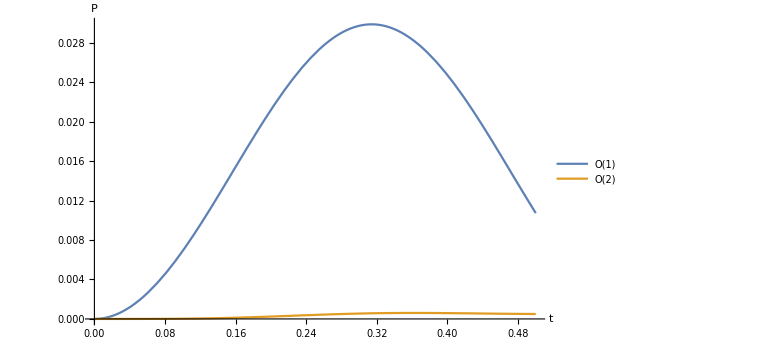

```mathematica
Plot[{FirstOrderTotalProb[t] ,SecondOrderTotalProb[t] },{t,0,tf},PlotLegends-> {"O(1)", "O(2)"},AxesLabel->{t,P},AxesStyle->Large,ImageSize->Large,PlotStyle-> Thick,LabelStyle->{Large,Black}(*,Ticks->{None,{0,0.5}}*),PlotRange->Full]
```

#### Electric field

```mathematica
ElectricFieldMatrixElements[p_,q_]:=Module[{ϕ1,ϕ2,a},
ϕ1=Φ[p];
ϕ2=Φ[q];
a=0;
If[ϕ1[[1;;NumberOfAtoms]]==ϕ2[[1;;NumberOfAtoms]],
a=Abs[ϕ1[[NumberOfAtoms+1]]-ϕ2[[NumberOfAtoms+1]]] 
];
a];

ElectricFieldMatrix = Table[ElectricFieldMatrixElements[p,q],{p,1,dimK},{q,1,dimK}];
```

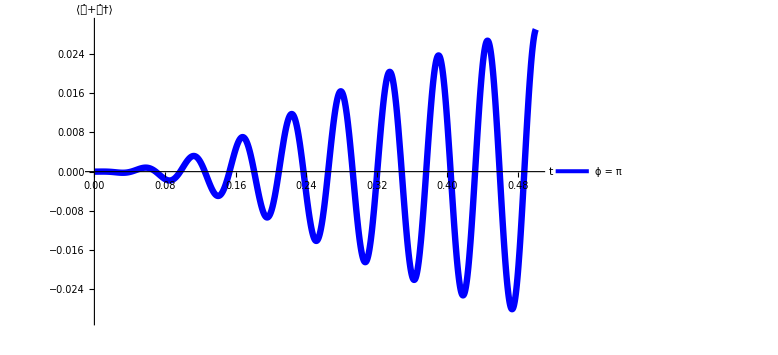

```mathematica
thick = 8 10^-3;
ϕ1=π;
ElectricField[ϕ_,t_]:=Chop[(Ψ[ϕ,t])*.ElectricFieldMatrix.(Ψ[ϕ,t]) ];
Plot[{ElectricField[ϕ1,t]},{t,t0,tf},PlotRange->{-0.03,0.03},AxesLabel->{t,Row@{AngleBracket["𝒶̂+𝒶̂†"]}},LabelStyle->Large,ImageSize->Large,PlotStyle-> {{Solid,Blue,Thickness[thick]}},PlotRange->{-0.3,0.3},PlotLegends->{Row@{"ϕ = ",ϕ1}},LabelStyle->{Large,Black}]
```

```mathematica
(*ωg1=0;
ωph=110;
Δ=10;
ωe1=ωg1+ωph+Δ;
υ=100;
ωe2=ωg1+Δ+υ;
ωg2=0;
IntPic=1;
Ω=1  ;
A= 1;*)
```

### Compiled Results

#### Heralding on Not G_2

-Graphics-

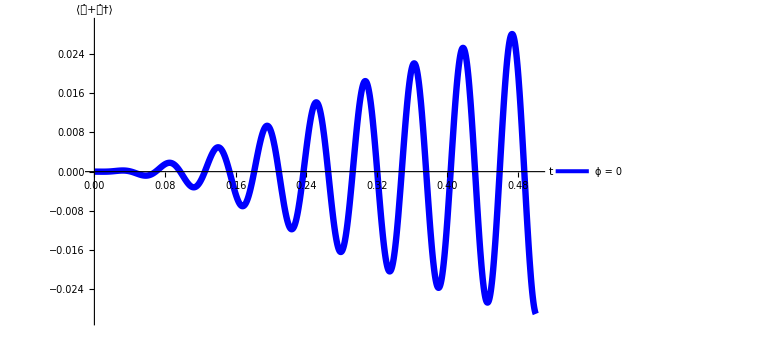

#### Heralding on Not G_1

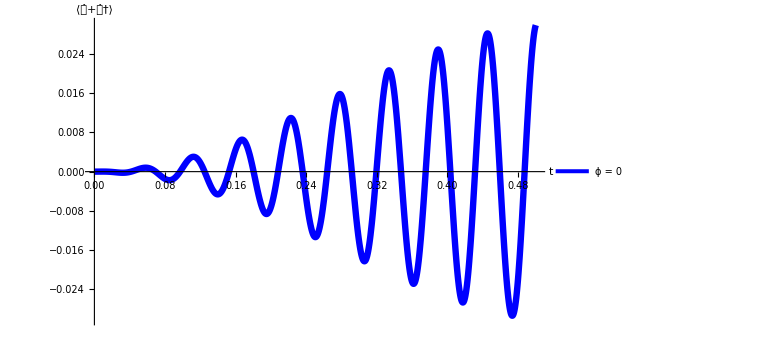

#### No Heralding